```mathematica
Practical 2
```

* Solve and Plot the following Differential Equations

```mathematica
Q1.y''+2y'-8y=0
```

```mathematica
sol1=DSolve[y''[x]+2*y'[x]-8*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^(2 x) C[2]}}

```mathematica
sol=y[x]/.sol1[[1]]/.{C[1]->2,C[2]->3}
```

2 ⅇ^(-4 x)+3 ⅇ^(2 x)

```mathematica
Plot[{sol3},{x,-3,3},PlotStyle->Red,Frame->True,AxesOrigin->{0,0},GridLines->Automatic]
```

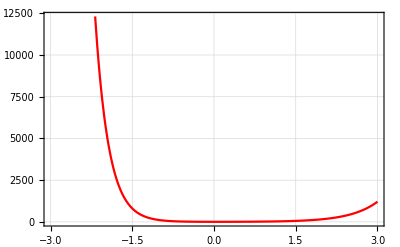

Q2. y”-y=0,y(0)=6,y’(0)=-2

```mathematica
sol2=DSolve[{y''[x]-y[x]==0,y[0]==6,y'[0]==-2},y[x],x]
```

{{y[x]→2 ⅇ^-x (2+ⅇ^(2 x))}}

```mathematica
Plot[y[x]/.sol2,{x,-2,2},PlotStyle->{Red},GridLines->Automatic]
```

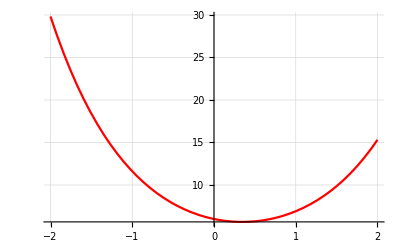

```mathematica
Q3.x^2y''+x*y'-4*y=0,y(1)=11,y'(1)=-6
```

```mathematica
q=DSolve[{x^2*y''[x]-x*y'[x]-4*y[x]==0,y[1]==11,y'[1]==-6},y[x],x]
```

{{y[x]→-1/10 x^(1-√5) (-55-17 √5-55 x^(2 √5)+17 √5 x^(2 √5))}}

```mathematica
Plot[y[x]/.q,{x,-2,2},PlotStyle->{Green},GridLines->Automatic]
```

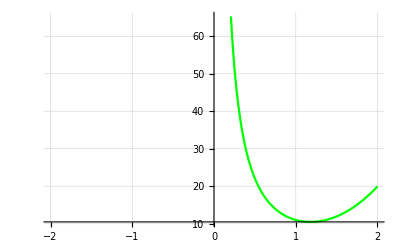

```mathematica
Q4.y''+y'-2y=x^2
```

```mathematica
r=DSolve[y''[x]+y'[x]-2*y[x]==x^2,y[x],x]
```

{{y[x]→1/4 (-3-2 x-2 x^2)+ⅇ^(-2 x) C[1]+ⅇ^x C[2]}}

```mathematica
r1=Table[y[x]/.r/.{C[1]->k,C[2]->2},{k,3,6}]
```

{{3 ⅇ^(-2 x)+2 ⅇ^x+1/4 (-3-2 x-2 x^2)},{4 ⅇ^(-2 x)+2 ⅇ^x+1/4 (-3-2 x-2 x^2)},{5 ⅇ^(-2 x)+2 ⅇ^x+1/4 (-3-2 x-2 x^2)},{6 ⅇ^(-2 x)+2 ⅇ^x+1/4 (-3-2 x-2 x^2)}}

```mathematica
Plot[{r1},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},GridLines->Automatic,Frame->True,AxesOrigin->{0,0}]
```

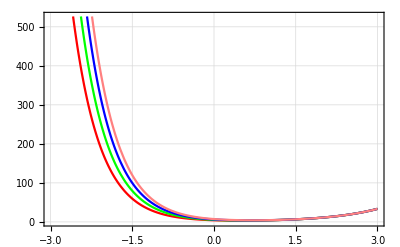

```mathematica
Q5.y''-5y'+6y=4*e^2x
```

```mathematica
sol5=DSolve[y''[x]-5*y'[x]+6*y[x]==4*(e^2x),y[x],x]
```

{{y[x]→1/9 (5 e^2+6 e^2 x)+ⅇ^(2 x) C[1]+ⅇ^(3 x) C[2]}}

```mathematica
SOL5=Table[y[x]/.sol5/.{C[1]->k,C[2]->2},{k,3,6}]
```

{{3 ⅇ^(2 x)+2 ⅇ^(3 x)+1/9 (5 e^2+6 e^2 x)},{4 ⅇ^(2 x)+2 ⅇ^(3 x)+1/9 (5 e^2+6 e^2 x)},{5 ⅇ^(2 x)+2 ⅇ^(3 x)+1/9 (5 e^2+6 e^2 x)},{6 ⅇ^(2 x)+2 ⅇ^(3 x)+1/9 (5 e^2+6 e^2 x)}}

```mathematica
Plot[{SOL5},{x,-3,3},PlotStyle->{Red,Green,Blue,Pink},GridLines->Automatic,Frame->True,AxesOrigin->{0,0}]
```

```mathematica
Q6.y''-16y=0,y(0)=3,y'(0)=8
```

```mathematica
p=DSolve[{y''[x]-16*y[x]==0,y[0]==3,y'[0]==8},y[x],x]
```

{{y[x]→1/2 ⅇ^(-4 x) (1+5 ⅇ^(8 x))}}

```mathematica
Plot[y[x]/.p,{x,-2,2},PlotStyle->Red,GridLines->Automatic]
```

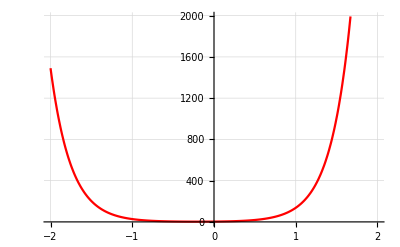

```mathematica
Q7.10y''-7y'+1.2y=0
```

```mathematica
sol7=DSolve[10*y''[x]-7*y'[x]+1.2*y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(0.3 x) C[1]+ⅇ^(0.4 x) C[2]}}

```mathematica
Sol=Table[y[x]/.sol7/.{C[1]->1,C[2]->k},{k,2,5}]
```

{{ⅇ^(0.3 x)+2 ⅇ^(0.4 x)},{ⅇ^(0.3 x)+3 ⅇ^(0.4 x)},{ⅇ^(0.3 x)+4 ⅇ^(0.4 x)},{ⅇ^(0.3 x)+5 ⅇ^(0.4 x)}}

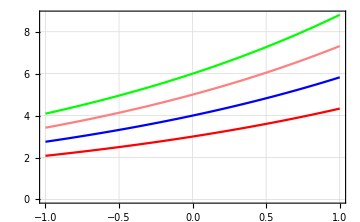

```mathematica
Plot[{Sol},{x,-1,1},PlotStyle->{Red,Blue,Pink,Green},GridLines->Automatic,Frame->True,AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
Q8.x^2y''+2xy'-6y=0
```

```mathematica
Sol8=DSolve[x^2*y''[x]+2*x*y'[x]-6*y[x]==0,y[x],x]
```

{{y[x]→x^2 C[1]+C[2]/x^3}}

```mathematica
SOL=Table[y[x]/.Sol8/.{C[1]->1,C[2]->k},{k,2,5}]
```

{{2/x^3+x^2},{3/x^3+x^2},{4/x^3+x^2},{5/x^3+x^2}}

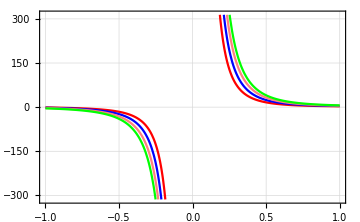

```mathematica
Plot[{SOL},{x,-1,1},PlotStyle->{Red,Blue,Pink,Green},GridLines->Automatic,Frame->True,AxesOrigin->{0,0},ImageSize->Medium]
```

```mathematica
Q9.x^2y''+xy'+4y=0
```

```mathematica
Sol9=DSolve[x^2*y''[x]+x*y'[x]+4*y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[2 Log[x]]+C[2] Sin[2 Log[x]]}}

```mathematica
SOL=Table[y[x]/.Sol9/.{C[1]->1,C[2]->k},{k,2,5}]
```

{{Cos[2 Log[x]]+2 Sin[2 Log[x]]},{Cos[2 Log[x]]+3 Sin[2 Log[x]]},{Cos[2 Log[x]]+4 Sin[2 Log[x]]},{Cos[2 Log[x]]+5 Sin[2 Log[x]]}}

```mathematica
Plot[{SOL},{x,-1,1},PlotStyle->{Red,Blue,Yellow,Green},GridLines->Automatic,Frame->True,AxesOrigin->{0,0}]
```

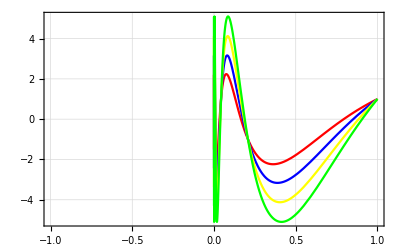

```mathematica
Q10.x^2y''-0.75y=0
```

```mathematica
Sol10=DSolve[x^2*y''[x]-0.75*y[x]==0,y[x],x]
```

{{y[x]→x^(-0.5+0. ⅈ) C[1]+x^(1.5+0. ⅈ) C[2]}}

```mathematica
SOL=Table[y[x]/.Sol10/.{C[1]->1,C[2]->k},{k,2,5}]
```

{{x^(-0.5+0. ⅈ)+2 x^(1.5+0. ⅈ)},{x^(-0.5+0. ⅈ)+3 x^(1.5+0. ⅈ)},{x^(-0.5+0. ⅈ)+4 x^(1.5+0. ⅈ)},{x^(-0.5+0. ⅈ)+5 x^(1.5+0. ⅈ)}}

```mathematica
Plot[{SOL},{x,-3,3},PlotStyle->{Blue,Red,Green,Yellow},Frame->True,AxesOrigin->{0,0},GridLines->Automatic,ImageSize->600]
```